```mathematica
tf=Import["D:\\document\\work\\volume-visualiser\\transferfuncs\\nucleon.tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
intensitycolors=Transpose[{intensity,colors}]
defaultcolorfunction=(Blend[{{0., RGBColor[0.05635, 0.081, 0.07687, 0.0166234]}, {0.1, RGBColor[0.8877, 0.2636, 0., 0.114961]}, {0.66, RGBColor[1., 0.9658, 0.4926, 0.665652]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & );
colorfunction=(Blend[intensitycolors, #1] & )
rgb=(#/255.&)/@Transpose[{r,g,b}];
colors2=RGBColor/@rgb;
intensitycolors2=Transpose[{intensity,colors2}]
colorfunction2=(Blend[intensitycolors2, #1] & )
```

{{0.141155,-Graphics-},{0.152678,-Graphics-},{0.172715,-Graphics-},{0.185807,-Graphics-},{0.411943,-Graphics-},{0.43787,-Graphics-},{0.4782,-Graphics-},{0.501154,-Graphics-},{0.786437,-Graphics-},{0.846932,-Graphics-},{0.94993,-Graphics-},{0.989554,-Graphics-}}

Blend[intensitycolors,#1]&

{{0.141155,-Graphics-},{0.152678,-Graphics-},{0.172715,-Graphics-},{0.185807,-Graphics-},{0.411943,-Graphics-},{0.43787,-Graphics-},{0.4782,-Graphics-},{0.501154,-Graphics-},{0.786437,-Graphics-},{0.846932,-Graphics-},{0.94993,-Graphics-},{0.989554,-Graphics-}}

Blend[intensitycolors2,#1]&

-Graphics3D-

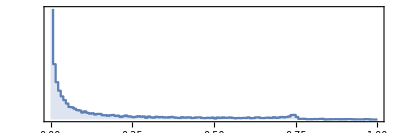

-Graphics-

```mathematica
volume=Import["D:\\_data\\nucleon.tif","Image3D"];
Image3D[volume,ColorFunction->colorfunction]
ImageHistogram[volume]
opacity=(#/255.&)/@a;
scalar=(#/255.&)/@intensity;
ListLinePlot[Transpose[{scalar,opacity}],ColorFunction->colorfunction2,PlotLegends->"volatility histogram"]
```

```mathematica
step=1/255.
o2=opacity
```

0.00392157

{0.,0.0431373,0.0431373,0.,0.,0.0509804,0.0509804,0.,0.,0.321569,0.32549,0.}

```mathematica
m=Mean[o2];
o2=If[#>m,#-step,#+step]&/@o2
```

{0.00392157,0.0470588,0.0470588,0.00392157,0.00392157,0.054902,0.054902,0.00392157,0.00392157,0.317647,0.321569,0.00392157}

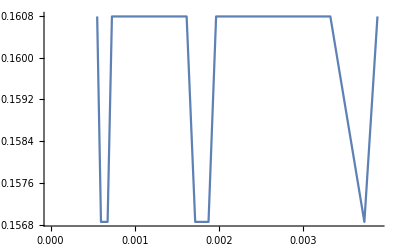

```mathematica
Do[m=Mean[o2];o2=If[#<0.000001,#,If[#>m,#-step,#+step]]&/@o2,{i,100}]
ListLinePlot[Transpose[{scalar,o2}]]
```